Having evaluated “Defining Transforms” in PSLSubs.nb

### useful stuff

```mathematica
PP=7;QQ=3;

resetdecorations :=
(disksize=.05;
closedQ=True;)
resetdecorations;
```

```mathematica
(*function returning graphics*)
path = Table[DiskGeodesicArc[{#[[i]],#[[Mod[i,Length[#]]+1]]}],{i,1,Length[#]+If[closedQ,0,-1]}]&;

(*function returning graphics*)
decorated:={PDiskCircle[#,disksize]&/@#,path@#}&;
```

```mathematica
mod[i_,n_:7]:=Mod[i-1,n]+1;
mod7=mod[#,7]&;

(*points*)
heptagon3=Table[
0∘Trans[ArcCosh[Cot[π/QQ//N] Cot[π/PP//N]]]∘Rot[2k Pi/PP],
{k,1,PP}];
```

```mathematica
(*points*)
heptamidpoints = Table[
#[[i]]∘Trans2Point[#[[i]],#[[Mod[i,Length[#]]+1]],DiskDistance[#[[i]],#[[Mod[i,Length[#]]+1]]]/2],
{i,Length[#]}]&@heptagon3;
```

```mathematica
heptagon3[[7]]
```

0.300743+0. ⅈ

```mathematica
(*points*)
heptastar = Table[heptamidpoints[[Mod[4i-1,7]+1]],{i,7}];
```

```mathematica
triangle={seven,three,two}={0,heptagon3[[7]],heptastar[[7]]};
(*transforms*)
gens = {α,β,γ}={gen7,gen3,gen2} ={ RotAboutPt[0,2Pi/7],RotAboutPt[heptagon3[[7]],2Pi/3],RotAboutPt[heptastar[[7]],2Pi/2]};

moregens = Union[gens, Table[power[gen7,k],{k,0,6}]];
```

```mathematica
Clear[words,wwords];
words[gens_,0]:={Ident}
words[gens,1]:=wwords[gens,1]=gens

words[gens_,k_:((#>0)&&IntegerQ[#]&)]:=words[gens,k]=
(wwords[gens,k]=Complement[
Join@@Outer[#1∘#2&,wwords[gens,k-1],gens],
words[gens,k-1],
Round[#1]===Round[#2]&
]; Union [wwords[gens,k],words[gens,k-1]])
```

### first model

```mathematica
heptastar2 = Table[heptamidpoints[[Mod[2i-1,7]+1]],{i,7}];
```

```mathematica
hexstars = Table[(#∘RotAboutPt[heptagon3[[i]],2Pi/3])&/@heptastar,
{i,7}];
```

```mathematica
fattenedarc[from_,to_,width_]:={
from∘Trans2Point[from,(to∘RotAboutPt[from,Pi/2]),width],
from∘Trans2Point[from,(to∘RotAboutPt[from,-Pi/2]),width],
to∘Trans2Point[to,(from∘RotAboutPt[to,Pi/2]),width],
to∘Trans2Point[to,(from∘RotAboutPt[to,-Pi/2]),width]};
```

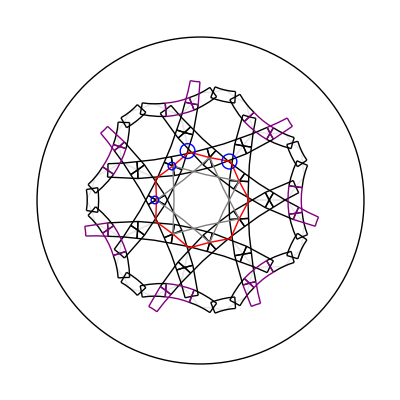

```mathematica
Graphics[resetdecorations;{Circle[{0,0},1],#}]&@

{closedQ=True;GrayLevel[.9],
Table[path@((#∘RotAboutPt[heptagon3[[i]],2Pi/3])&/@heptagon3),{i,7}],

widthh=.126;

Black,
Table[
{path@fattenedarc[#[[i]],#[[Mod[i,7]+1]],widthh]&@heptamidpoints(*,
path@((#∘RotAboutPt[heptastar2[[1]],Pi]∘RotAboutPt[0,2Pi i/7])&/@(fattenedarc[#[[1]],#[[Mod[1,7]+1]],widthh]&@heptastar2)),


path@((#∘RotAboutPt[heptastar2[[2]],Pi]∘RotAboutPt[0,2Pi i/7])&/@(fattenedarc[#[[1]],#[[Mod[1,7]+1]],widthh]&@heptastar2))*)},{i,7}],


Table[path@(#∘RotAboutPt[0,2Pi i /7]∘RotAboutPt[heptastar2[[2]],Pi]∘RotAboutPt[0,2Pi k /7]&/@
(fattenedarc[#[[1]],#[[Mod[1,7]+1]],widthh]&@heptamidpoints)),{i,7},{k,7}],
Thick,Purple,Table[{path@((#∘RotAboutPt[0, 2Pi  /7]∘RotAboutPt[heptastar2[[1]],Pi]∘RotAboutPt[heptastar2[[7]],Pi]∘RotAboutPt[0,2Pi i/7])&/@
(fattenedarc[#[[1]],#[[Mod[1,7]+1]],widthh]&@heptamidpoints)),
path@((#∘RotAboutPt[0, 2Pi  /7]∘RotAboutPt[0, 2Pi  /7]∘RotAboutPt[heptamidpoints[[2]],Pi]∘RotAboutPt[heptastar2[[7]],Pi]∘RotAboutPt[0,2Pi i/7])&/@
(fattenedarc[#[[1]],#[[Mod[1,7]+1]],widthh]&@heptamidpoints))
},{i,7}],Thick,Red,path@heptagon3,Thin, Gray,path@heptastar2,
Thick,Blue,
PDiskCircle[Real2Comp[coordconvert[#]],.1]&/@({{295,191},{231,175}}),
PDiskCircle[Real2Comp[coordconvert[#]],.05]&/@{{207,198},{181,250}},

(*path @ heptamidpoints,*)


}
```

```mathematica
coordconvert= #{1,-1}/250+{-1,1}&;
```

```mathematica
{{207,198},{181,250}}
```

{{207,198},{181,250}}

```mathematica
(Real2Comp[coordconvert[#]]&/@({{500,500},{0,500}}))
```

{1-ⅈ,-1-ⅈ}

```mathematica
(*as a test; this should be approximately 2A*)
DiskDistance@@(Real2Comp/@(coordconvert/@{{295,191},{231,175}}))
```

0.573311

```mathematica
(*as a test; this should be approximately B*)
```

```mathematica
DiskDistance@@(Real2Comp/@(coordconvert/@{{207,198},{181,250}}))
```

0.497405

```mathematica
coshA=Cos[Pi/7]/Sin[Pi/3]
```

(2 Cos[π/7])/(√3)

```mathematica
sinhA=√(coshA^2-1)//Simplify;
A=ArcCosh[coshA]//N
```

0.283128

```mathematica
2A (*this checks out*)
```

0.566256

```mathematica
coshB = coshA^2 - Cos[2Pi/3](sinhA^2)//Simplify
```

```mathematica
sinhB=√(coshB^2-1)//Simplify;

B=ArcCosh[coshB]//N (*this checks out too*)
```

0.491993

```mathematica
coshB2=Cosh[ArcCosh[coshB]/2];
```

```mathematica
B2=N@ArcCosh[coshB2]
```

0.868853

```mathematica
cosg=(coshA coshB - coshA)/(sinhA sinhB)//Simplify
```

2 Cos[π/7] √((-1+2 Sin[(3 π)/14])/(-1-2 Sin[π/14]+4 Sin[(3 π)/14]))

```mathematica
g=ArcCos[cosg] 180./Pi (*within just one degree of 30° -- within public partipation art error*)
```

29.0284

```mathematica
coshD = coshA coshB2 -(sinhA √(coshB2^2-1))cosg//Simplify
```

-(2 Cos[π/7] (-Cosh[1/2 ArcCosh[1/2+Sin[(3 π)/14]]]+((-1+2 Sin[(3 π)/14]) Sinh[1/2 ArcCosh[1/2+Sin[(3 π)/14]]])/(√(-1-2 Sin[π/14]+4 Sin[(3 π)/14]))))/(√3)

```mathematica
Dd=ArcCosh[coshD]//N
```

0.138783

```mathematica
ArcCosh[cosg/Sin[Pi/3.]]
```

0.138783

```mathematica
B/Dd 10
```

35.4505

```mathematica
(*We can now say with some confidence that D is about .138783, that the angle g is about 29°. The relative width and length of B and D is an awkard 3.54ish *)
```

### second model

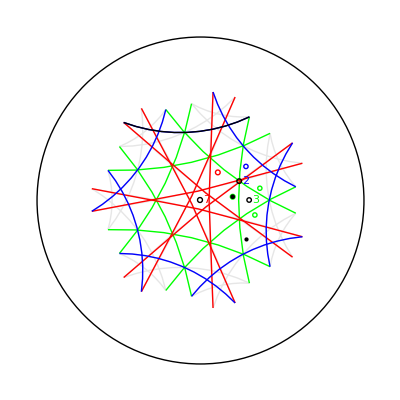

```mathematica
Graphics[resetdecorations;{Circle[{0,0},1],#}]&@

{GrayLevel[.9],closedQ=True;

(*path @ heptamidpoints,*)

path@heptastar,

path/@(hexstars = Table[(#∘RotAboutPt[heptagon3[[i]],2Pi/3])&/@heptastar,
{i,7}]),


Green,
(*DiskGeodesicArc[{hexstars[[1,5]],hexstars[[4,5]]}],*)
Table[
DiskGeodesicArc[{hexstars[[i,mod7@(2i+3)]],hexstars[[mod7@(i+3),mod7@(2 i+3)]]}],{i,7}],
Red,
Table[
DiskGeodesicArc[{hexstars[[i,Mod[2i-1-1,7]+1]],hexstars[[Mod[i+3-1,7]+1,Mod[2 i-1,7]+1]]}],{i,7}],
Blue,
Table[
(DiskGeodesicArc[{hexstars[[#[[1,1]],#[[1,2]]]],hexstars[[#[[2,1]],#[[2,2]]]]}])&@(mod@({{1+k,3+2k},{7+k,4+2k}})),
{k,7}],


Black,
PDiskCircle[#,.03]&/@triangle,


pppt=(.2+.02I);


Red,
PDiskCircle[#,.03]&/@((pppt∘#)&/@{RotAboutPt[triangle[[1]],2Pi/7]}),
Text[#[[1]],{Re[#],Im[#]}&@#[[2]]]&@{7,triangle[[1]]+.04},

Green,

PDiskCircle[#,.03]&/@((pppt∘#)&/@Table[RotAboutPt[triangle[[2]],2k Pi/3],{k,0,2}]),
Text[#[[1]],{Re[#],Im[#]}&@#[[2]]]&@{3,triangle[[2]]+.04},

Blue,
PDiskCircle[#,.03]&/@((pppt∘#)&/@{RotAboutPt[triangle[[3]],2Pi/2]}),
Text[#[[1]],{Re[#],Im[#]}&@#[[2]]]&@{2,triangle[[3]]+.04},
Black,

PDisk[#,.03]&/@((pppt∘#)&/@{Ident,α∘β}),

motion=gen3∘gen2;
With[{k=2},
(DiskGeodesicArc[
#∘motion&/@#&/@
{hexstars[[#[[1,1]],#[[1,2]]]],hexstars[[#[[2,1]],#[[2,2]]]]}])&@(
(mod@({{1+k,3+2k},{7+k,4+2k}})))]



(*(DiskGeodesicArc[{hexstars[[#[[1,1]],#[[1,2]]]],hexstars[[#[[2,1]],#[[2,2]]]]}])&/@

{{{1,3},{7,4}},{{2,5},{1,6}}}*)
}
```

### larger model

```mathematica
With[{ppt={.17,.07}},(*Let's try making a Cayley graph, with this as the master vertex*)


motions = {Ident};

Graphics[
pppt = Real2Comp@ppt;
resetdecorations; (*whatever one wants*)
{Circle[{0,0},1],#}]&@

{Red, PDisk[pppt,.03],
PDiskCircle[#,.03]&/@((pppt∘#)&/@
(words[gens,4];wwords[gens,4])),
Black,
DiskGeodesicArc[{pppt∘#[[1]],pppt∘#[[2]]}]&/@
{{Ident,α}∘#,{Ident,β}∘#}&/@wwords[gens,4]
}]
(*,{ppt,{.17,.07},Locator}]*)
```

Join::heads: Heads Function and List at positions 1 and 2 are expected to be the same.

Complement::heads: Heads List and Join at positions 2 and 1 are expected to be the same.

Join::heads: Heads Function and Complement at positions 1 and 2 are expected to be the same.

Complement::heads: Heads Union and Join at positions 2 and 1 are expected to be the same.

Join::heads: Heads Function and Complement at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Complement::heads: Heads Union and Join at positions 2 and 1 are expected to be the same.

General::stop: Further output of Complement::heads will be suppressed during this calculation.

CompiledFunction::cfsa: Argument (0.17+0.07 ⅈ)∘Join[#1∘#2&,«1»,{|0.900969+0.433884 ⅈ,0.+0. ⅈ|,|0.454777+«1»,«1»|,|5.77629×10^-17+1.0708 ⅈ,0.230893+0.479455 ⅈ|}] at position 1 should be a machine-size complex number.

CompiledFunction::cfsa: Argument (0.17+0.07 ⅈ)∘(Complement[«1»]∪«1»∪{|0.900969+0.433884 ⅈ,0.+0. ⅈ|,|«19»+«18» ⅈ,0.+«1»|,|5.77629×10^-17+1.0708 ⅈ,0.230893+0.479455 ⅈ|}) at position 1 should be a machine-size complex number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

-Graphics-

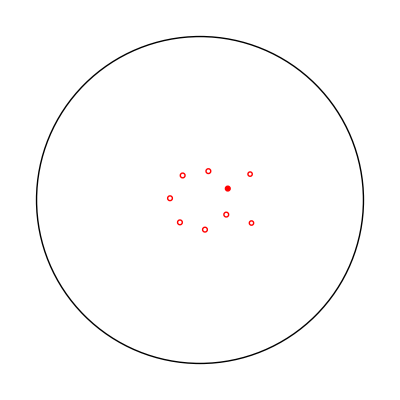

```mathematica
With[{ppt={.17,.07}},(*Let's try making a Cayley graph*)
motions = {Ident,α};

Graphics[
pppt = Real2Comp@ppt;
resetdecorations;{


Circle[{0,0},1],#}]&@

{Red, PDisk[pppt,.03],
PDiskCircle[#,.03]&/@
((pppt∘#)&/@
(subonlytodepth[moregens,1]))

}]
```

```mathematica
2
```